Name : Karan Sharma
College Roll No. : 2232191
University Roll No. : 22036563079
Course : B.SC(H) Mathematics /3rd Year/ Complex Analysis
Section : A

PRACTICAL 12 : ML - inequality                                                                                 

Q-). Use ML-inequality to show that       |∫_c^□ 1/(z^2+1)ⅆz| ≤1/5,
                        where C is the line segment form 2 to 2 + ⅈ. While solving, represent the distance from the point z to the points ⅈ and -ⅈ, respectively.

Given function

```mathematica
f[z_]:=1/(z^2+1)
```

Given curve

```mathematica
c[t_]:=2+ⅈ t
```

Computation of the modulus of the given function by plugging in the z value given in the curve.

```mathematica
k[t_]:=ComplexExpand[f[c[t]]]
```

```mathematica
r[t_]=Refine[Re[k[t]],t∈Reals]
```

5/(16 t^2+(5-t^2)^2)-t^2/(16 t^2+(5-t^2)^2)

```mathematica
s[t_]=Refine[Im[k[t]],t∈Reals]
```

-(4 t)/(16 t^2+(5-t^2)^2)

```mathematica
A[t_]=Simplify[√(s[t]^2+r[t]^2)]
```

√(1/(25+6 t^2+t^4))

M - value

```mathematica
M=MaxValue[{A[t],0≤t≤1},t]
```

1/5

Length of the Curve

```mathematica
L=∫_0^1 Abs[c'[t]]ⅆt
```

1

```mathematica
Print["An upper bound to the absolule value of the integral |∫_c^□ 1/z^2ⅆz| is found to be ",M*L,"."]
```

An upper bound to the absolule value of the integral |∫_c^□ 1/z^2ⅆz| is found to be 1/5.

Plotting of the random point on the given curve

```mathematica
p={2,RandomReal[{0,1}]}
```

{2,0.696944}

Representing the distance from the random point to the points ⅈ and -ⅈ

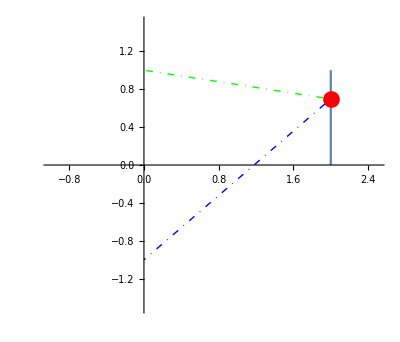

```mathematica
a=ParametricPlot[{Re[c[t]],Im[c[t]]},{t,0,1},PlotRange->{{-1,2.5},{-1.5,1.5}}];
b=Graphics[{Red,PointSize[0.03],Point[p],Green,DotDashed,Line[{p,{0,1}}],Blue,DotDashed,Line[{p,{0,-1}}]}];
Show[a,b]
```